Units used: GeV for masses, ps for lifetimes, cm for distances

```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookSave[];
```

```mathematica
SetDirectory[ NotebookDirectory[]]
```

/home/stasya/prj/alps-BelleII

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
```

### Display

Short-Hands to give all plots a consistent look and collect labels that will be used several times

```mathematica
colours={ColorData[10,6],ColorData[10,1],ColorData[10,5],ColorData[10,3],ColorData[10,8],ColorData[10,2],ColorData[10,7],ColorData[10,4],ColorData[10,9]}
```

{RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275]}

```mathematica
styles={Directive[colours[[1]],Dashed],Directive[colours[[2]],Dashed],Directive[colours[[1]],Dotted],colours[[2]],colours[[1]],colours[[3]],colours[[4]],colours[[5]]};
```

```mathematica
styles
```

{Directive[RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],Dashing[{Small,Small}]],Directive[RGBColor[0.6980392156862745, 0.01568627450980392, 0.],Dashing[{Small,Small}]],Directive[RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],Dashing[{0,Small}]],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333]}

```mathematica
legends={"K_S, m_a=0.3GeV","K_S, m_a=0.05GeV", "D, m_a=0.3GeV", "B^+, m_a=0.05GeV", "B^+, m_a=0.3GeV", "B^+, m_a=1GeV", "B^+, m_a=2GeV", "B^+, m_a=4GeV"};
```

```mathematica
disp={PlotStyle->styles,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
dispH={ChartLegends->legends,ChartStyle->styles,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
```

```mathematica
basicdisp={AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10]};
```

```mathematica
xgrid=Table[Log[i*10^(j)],{j,-10,10},{i,1,9}]//Flatten//N//Sort;
```

### Belle II parameters

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
τK=10^12 1.238*10^-8;(*ps*)
ΓtotalK=6.582*10^-25/(10^-12 τK);(*GeV*)
cτK=3 10^10 10^-12 τK(*in cm*);
```

All γβB is now actually γB

```mathematica
Belle2params={γβB:>1.03029,RCDC:>60,θCDCMin:>17 Degree, θCDCMax:>150 Degree,dres:>0.9,NBBBelleII:>5*10^10};
Belleparams={γβB:>1.08657,RCDC:>86.3,θCDCMin:>17 Degree, θCDCMax:>150 Degree,dres:>10^-4 500,NBBBelle:>5*10^10/50};
```

```mathematica
Sin[150 Degree//N]
```

0.5

```mathematica
dres/.Belle2params//N
```

0.9

### Init/form factors

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24,v-> 246.22};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07,Λ-> 4 π 10^3};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,MB:>4.18,mb:>4.18,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MT:>173,mt:>173,MS:>0.095,ms:>0.095,mB:>5.279,mK:>0.4937,mπ:>0.14,mD:>1.86,v:>246,me:>0.000511,mμ:>0.106,mτ:>1.777,MD:>0.0047,md:>0.0047,Γh:>0.013,mBs:>5.367,fBs:>0.227,mBd:>5.280,fBd:>0.188,vev:>246.22, mKstarV892:>0.892, mKstarV1410:>1.41, mKstarV1680:>1.72,mKAV1270:>1.27,mKAV1400:>1.4,mKstarS700:>0.7,mKstarS1430:>1.43};

ckms={CKM[3,3]:>0.999,Vtb:>0.999,CKM[3,2]:>0.0404,Vts:>0.0404,CKM[2,3]:>0.0412,Vcb:>0.0412,CKM[2,2]:>0.973,Vcs:>0.973, Vtd:> 8.1/1000};
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181,Subscript[X,t]:>1.469,sw.b2:>0.231};
eulergamma={Subscript[γ,E]:>0.5772};
```

### Geometrical integration over detector

```mathematica
(*γβ[γβParent_,mParent_,mϕ_]:=γβParent mParent/(2 mϕ)/.formFactors/.values/.masses/.couplings/.ckms*)
```

γβParent is actually γBParent

```mathematica
γβ[γParent_,mParent_,mϕ_]:=√(γParent^2 ((mB^2-mK^2+mϕ^2)^2)/(4 mB^2 mϕ^2)-1)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
θminBoost[θmin_,r_,cτ_,γβ_]:=ArcTan[r/(r/Tan[θmin]-γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
θmaxBoost[θmax_,r_,cτ_,γβ_]:=π+ArcTan[-r/(-r/Tan[θmax]+γβ cτ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
GeomInt[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=1/(4(γβ  cτ)^2)NIntegrate[1/Sin[θ](ⅇ^(-dmin/(Sin[θ] γβ  cτ))(dmin^2+2 γβ  cτ Sin[θ](dmin+γβ  cτ Sin[θ]) )-ⅇ^(-dmax/(Sin[θ] γβ cτ))(dmax^2+2 γβ  cτ Sin[θ](dmax+γβ  cτ Sin[θ]) ))/.formFactors/.values/.masses/.couplings/.ckms,{θ,θmin,θmax}]
```

```mathematica
GeomIntNewPart[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=1/(4(γβ  cτ)^2)NIntegrate[1/Sin[θ](ⅇ^(-dmin/(Sin[θ] γβ  cτ))(dmin^2+2 γβ  cτ Sin[θ](dmin) )-ⅇ^(-dmax/(Sin[θ] γβ cτ))(dmax^2+2 γβ  cτ Sin[θ](dmax) ))/.formFactors/.values/.masses/.couplings/.ckms,{θ,θmin,θmax}]
```

```mathematica
γβϕB[mϕ_]:=γβ[γβB,mB,mϕ]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
GeomIntCDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
GeomIntBelleIICDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=ReplaceAll[Belle2params][HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms];
```

```mathematica
GeomIntBelleCDC[θmin_,θmax_,dmin_,dmax_,cτ_,γβ_]:=ReplaceAll[Belleparams][HeavisideTheta[Re[RCDC/Tan[θmin]-γβB cτB]]GeomInt[θmin,θmax,dmin,dmax,cτ,γβ]/.formFactors/.values/.masses/.couplings/.ckms];
```

```mathematica
expDecay[d_,θ_,mϕ_,α_,BRDM_]:=Exp[-d/(Sin[θ] γβ[γβB,mB,mϕ] cτϕBRDM[mϕ,α,BRDM])]/.HeavisideTheta[0]:>1/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

### Γ(Alp) and effective ALP-SM couplings

Only electrons and muons so far

```mathematica
αsdata=ImportString["1.50, 0.349
1.60, 0.335
1.87, 0.313
2.04, 0.301
2.33, 0.282
2.68, 0.266
3.18, 0.249
3.97, 0.229
5.13, 0.212
6.86, 0.196
9.67, 0.180
13.2, 0.168
20.2, 0.153
29.5, 0.142
45.3, 0.132
73.2, 0.122
114, 0.114
201, 0.106
361, 0.0985
603, 0.0932
1.18e+3, 0.0870
2.06e+3, 0.0823
"] (*PDG*);
```

```mathematica
αsdata[[1,1]]
```

1.5

```mathematica
αs[Q_]:=Interpolation[αsdata][Q]HeavisideTheta[Q-αsdata[[1,1]]]
```

InterpolatingFunction::dmval: Input value {0.00100019} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00120702} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00145662} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

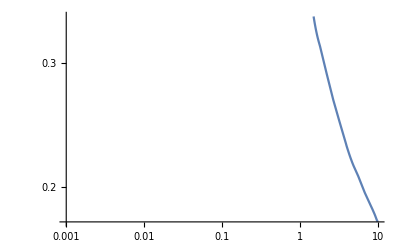

```mathematica
LogLogPlot[αs[q],{q,10^-3,10},PlotRange->Full]
```

```mathematica
(*αs[Q_]:=Interpolation[ImportString[StringReplace[Import["Experimental_files/alphaStab.dat","Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"]][Q]*)
```

```mathematica
mQ[ma_]:=mQ/.masses; (*quark mass running not included so far*)
```

```mathematica
nq[ma_]:=(HeavisideTheta[ma-MU]+HeavisideTheta[ma-MD]+HeavisideTheta[ma-MS]+HeavisideTheta[ma-MC]+HeavisideTheta[ma-MB])
```

```mathematica
T3[mf_]:=1/2 KroneckerDelta[mf,MU]+1/2 KroneckerDelta[mf,MC]+1/2 KroneckerDelta[mf,MT]-1/2 KroneckerDelta[mf,MD]-1/2 KroneckerDelta[mf,MS]-1/2 KroneckerDelta[mf,MB]-1/2 KroneckerDelta[mf,me]-1/2 KroneckerDelta[mf,mμ]-1/2 KroneckerDelta[mf,mτ]
```

```mathematica
f[τ_]:=If[τ<1,π/2+ⅈ/2 Log[(1+√(1-τ))/(1-√(1-τ))],ArcSin[1/(√τ)]]
B1[τ_]:=(1-τ f[τ]^2)/.constants/.values/.masses
```

```mathematica
Γalpff[ma_,ml_,cc_]:=(ml^2 Abs[cffEff[cc,Λ,ml]]^2)/(8 π Λ^2)√(ma^2-4 ml^2)HeavisideTheta[ma-2 ml];
ΓalpQQ[ma_,mQ_,cc_,ma_]:=(3  mQ[ma]^2 Abs[cffEff[cc,Λ,mQ]]^2)/(8 π Λ^2)√(ma^2-4 mQ^2)HeavisideTheta[ma-2 mQ];
Γalpγγ[ma_,cc_]:=((1/137)^2 ma^3)/(64 π^3(Λ/(4 π))^2)Abs[cγγEff[cc,ma]]^2;
ΓalpHadr[ma_,cc_]:=(32 π αs[ma]^2 ma^3)/Λ^2(1+(97/4-(7 nq[ma])/6)αs[ma]/π)Abs[cGGEff[cc,ma]]^2;
```

```mathematica
Γalp[ma_,cc_]:=Γalpff[ma,me,cc]+Γalpff[ma,mμ,cc]+Γalpff[ma,mτ,cc]+Γalpγγ[ma,cc]+ΓalpHadr[ma,cc];
```

```mathematica
τa[ma_,cc_]:=10^12(Γalp[ma,cc] GevToInverseSec)^-1/.constants (*in psc*)
cτa[ma_,cc_]:=3 10^10 10^-12 τa[ma,cc](*in cm*)
```

```mathematica
cffEff[cc_,Λ_,mf_]:=cc(1-(1-KroneckerDelta[mf,(MB/.masses)]/6)(3(√2 MT/v)^2)/(8 π^2)T3[mf]Log[Λ^2/MT^2]);
cγγEff[cc_,Λ_]:=cc(3 (2/3)^2(HeavisideTheta[Λ-MU]+HeavisideTheta[Λ-MC]+HeavisideTheta[Λ-MT])+3 (1/3)^2(HeavisideTheta[Λ-MD]+HeavisideTheta[Λ-MS]+HeavisideTheta[Λ-MB])+(HeavisideTheta[Λ-me]+HeavisideTheta[Λ-mμ]+HeavisideTheta[Λ-mτ]))
cγγEffGen[cc_,Λ_]:=cc(3 (2/3)^2(HeavisideTheta[Λ-MU]B1[(4 MU^2)/Λ^2]+HeavisideTheta[Λ-MC]B1[(4 MC^2)/Λ^2]+HeavisideTheta[Λ-MT]B1[(4 MT^2)/Λ^2])+3 (1/3)^2(HeavisideTheta[Λ-MD]B1[(4 MD^2)/Λ^2]+HeavisideTheta[Λ-MS]B1[(4 MS^2)/Λ^2]+HeavisideTheta[Λ-MB]B1[(4 MB^2)/Λ^2])+(HeavisideTheta[Λ-me]B1[(4 me^2)/Λ^2]+HeavisideTheta[Λ-mμ]B1[(4 mμ^2)/Λ^2]+HeavisideTheta[Λ-mτ]B1[(4 mτ^2)/Λ^2]))
cGGEff[cc_,Λ_]:=cc/2(HeavisideTheta[Λ-MU]+HeavisideTheta[Λ-MC]+HeavisideTheta[Λ-MT]+HeavisideTheta[Λ-MD]+HeavisideTheta[Λ-MS]+HeavisideTheta[Λ-MB])
```

```mathematica
Re[B1[(4 m^2)/Λ^2].values/.masses/.m-> 10//N]
```

Re[(1.00012-0.000056788 ⅈ).{α_(0,fzero):>0.329,α_(1,fzero):>0.195,α_(2,fzero):>-0.446,α_(0,fplus):>0.329,α_(1,fplus):>-0.876,α_(2,fplus):>0.006,α_(0,Azero):>0.343,α_(1,Azero):>-1.13,α_(2,Azero):>2.326,10._(R,fzero):>5.54,10._(R,fplus):>5.325,10._(R,Azero):>5.279,F0BS700:>0.46,aS700:>1.6,bS700:>1.35,F0BS1430:>0.17,aS1430:>4.4,bS1430:>6.4,F0A:>0.22,F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34. 0.0174533,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07,Λ→12566.4}]

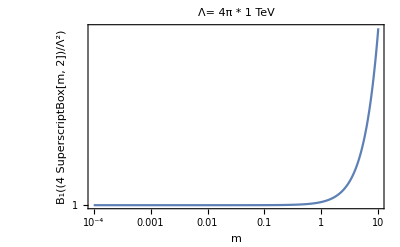

```mathematica
LogLogPlot[{Re[B1[(4 m^2)/Λ^2]/.values/.masses//N],Im[B1[(4 m^2)/Λ^2]/.values/.masses//N]},{m,10^-4,10},Frame->True,PlotRange->All,FrameLabel->{"m","B_1((4 SuperscriptBox[m, 2])/Λ^2)"},PlotLabel->"Λ= 4π * 1 TeV"]
```

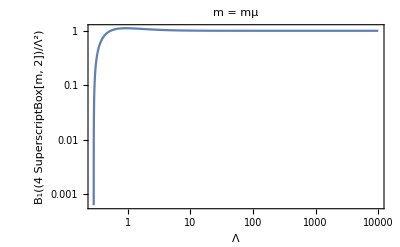

```mathematica
LogLogPlot[{Re[B1[(4 mμ^2)/λ^2]/.values/.masses//N],Im[B1[(4 mμ^2)/λ^2]/.values/.masses//N]},{λ,10^-4,10^4},Frame->True,PlotRange->All,FrameLabel->{"Λ","B_1((4 SuperscriptBox[m, 2])/Λ^2)"},PlotLabel->"m = mμ"]
```

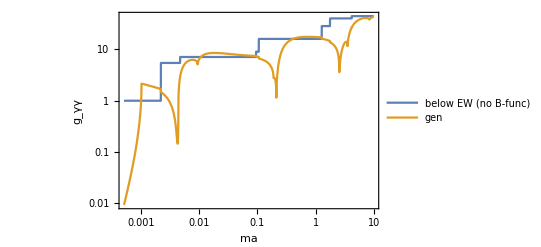

```mathematica
LogLogPlot[{Abs[cγγEff[1,ma]]^2/.values/.masses,Abs[cγγEffGen[1,ma]]^2/.values/.masses},{ma,10^-4,10},Frame->True,PlotRange->All,PlotLegends->{"below EW (no B-func)","gen"},FrameLabel->{"ma","g_γγ"}]
```

```mathematica
Γalpγγ[1,1]/.values/.masses//N
```

4.29585×10^-13

```mathematica
ΓalpHadr[2,1]/.values/.masses//N
```

5.43772×10^-6

```mathematica
ΓalpHadr[5,1]/.values/.masses//N
```

0.0000509222

```mathematica
Γalpff[1,me,1]/.values/.masses
```

8.86932×10^-17

InterpolatingFunction::dmval: Input value {0.000100024} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

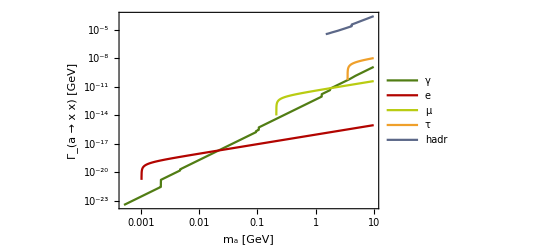

alp-decay-rates.png

```mathematica
LogLogPlot[{Γalpγγ[ma,1]/.values/.masses,Γalpff[ma,me,1]/.values/.masses,Γalpff[ma,mμ,1]/.values/.masses,Γalpff[ma,mτ,1]/.values/.masses,ΓalpHadr[ma,1]/.values/.masses},{ma,10^-4,10},PlotLegends->{"γ","e","μ","τ","hadr","all"},PlotStyle->colours,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],PlotRange->All,Frame->True,FrameLabel->{"m_a [GeV]","Γ_(a →  x x) [GeV]"}]
Export["alp-decay-rates.png",%];
```

```mathematica
Γalpγγ[0.1,1]/.values/.masses
```

2.41642×10^-16

```mathematica
ΓalpHadr[0.1,1]/.values/.masses//N
```

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.

```mathematica
Γalp[0.1,1]/.values/.masses
```

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.42529×10^-16+0. ⅈ

```mathematica
Γalpff[10,mτ,1].values/.masses
```

(11.7439 Abs[1+(29929 Log[Λ^2/29929])/(161376 π^2)]^2)/Λ^2.{α_(0,fzero):>0.329,α_(1,fzero):>0.195,α_(2,fzero):>-0.446,α_(0,fplus):>0.329,α_(1,fplus):>-0.876,α_(2,fplus):>0.006,α_(0,Azero):>0.343,α_(1,Azero):>-1.13,α_(2,Azero):>2.326,m_(R,fzero):>5.54,m_(R,fplus):>5.325,m_(R,Azero):>5.279,F0BS700:>0.46,aS700:>1.6,bS700:>1.35,F0BS1430:>0.17,aS1430:>4.4,bS1430:>6.4,F0A:>0.22,F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 °,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07,Λ→4000 π}

InterpolatingFunction::dmval: Input value {0.000100024} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {0.000126515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

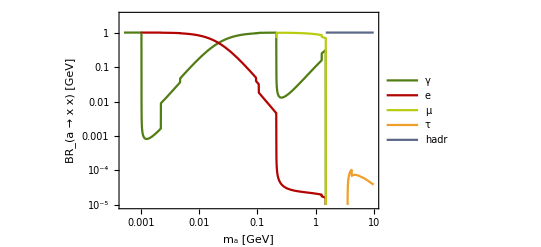

alp-BR.png

```mathematica
LogLogPlot[{Γalpγγ[ma,1]/Γalp[ma,1]/.values/.masses,Γalpff[ma,me,1]/Γalp[ma,1]/.values/.masses,Γalpff[ma,mμ,1]/Γalp[ma,1]/.values/.masses,Γalpff[ma,mτ,1]/Γalp[ma,1]/.values/.masses,ΓalpHadr[ma,1]/Γalp[ma,1]/.values/.masses},{ma,10^-4,10},PlotLegends->{"γ","e","μ","τ","hadr"},PlotStyle->colours,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],PlotRange->{Automatic,{10^-5,3}},Frame->True,FrameLabel->{"m_a [GeV]","BR_(a →  x x) [GeV]"}]
Export["alp-BR.png",%];
```

InterpolatingFunction::dmval: Input value {0.000100024} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

InterpolatingFunction::dmval: Input value {0.000126515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

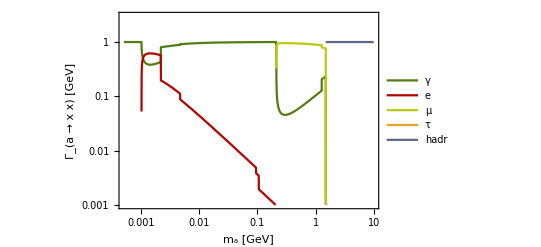

```mathematica
LogLogPlot[{Γalpγγ[ma,1/(4π)]/Γalp[ma,1/(4π)]/.values/.masses,Γalpff[ma,me,1/(4π)]/Γalp[ma,1/(4π)]/.values/.masses,Γalpff[ma,mμ,1/(4π)]/Γalp[ma,1/(4π)]/.values/.masses,Γalpff[ma,mτ,1/(4π)]/Γalp[ma,1/(4π)]/.values/.masses,ΓalpHadr[ma,1/(4π)]/Γalp[ma,1/(4π)]/.values/.masses},{ma,10^-4,10},PlotLegends->{"γ","e","μ","τ","hadr"},PlotStyle->colours,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],PlotRange->{Automatic,{10^-3,3}},Frame->True,FrameLabel->{"m_a [GeV]","Γ_(a →  x x) [GeV]"}]
```

InterpolatingFunction::dmval: Input value {0.000100024} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

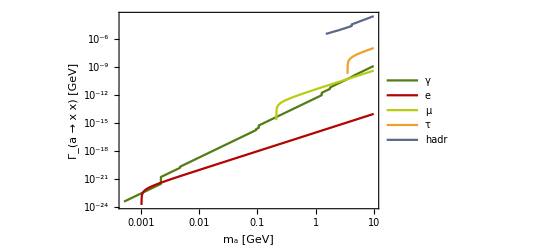

alp-decay-rates.png

```mathematica
LogLogPlot[{Γalpγγ[ma,1]/.values/.masses,Γalpff[ma,me,1]/.values/.masses,Γalpff[ma,mμ,1]/.values/.masses,Γalpff[ma,mτ,1]/.values/.masses,ΓalpHadr[ma,1]/.values/.masses},{ma,10^-4,10},PlotLegends->{"γ","e","μ","τ","hadr"},PlotStyle->colours,AxesStyle->Directive[Black,10],LabelStyle->Directive[Black,10],PlotRange->All,Frame->True,FrameLabel->{"m_a [GeV]","Γ_(a →  x x) [GeV]"}]
Export["alp-decay-rates.png",%]
```

### ALP production branching fractions

```mathematica
BRBtoKPa[ma_,gabs_]:=1/ΓtotalB mB^3/(16 π) Abs[gabs]^2(1-mK^2/mB^2)^2 fzero[ma^2]^2 √((1-(ma+mK)^2/mB^2)(1-(ma-mK)^2/mB^2)) /.constants/.formFactors/.values/.masses/.ckms
BRKtoπPa[ma_,gabs_]:=1/ΓtotalK mK^3/(16 π) Abs[gabs]^2(1-mπ^2/mK^2)^2 f0Kπ[ma^2]^2 √((1-(ma+mπ)^2/mK^2)(1-(ma-mπ)^2/mK^2)) /.constants/.formFactors/.values/.masses/.ckms (*1901.02031*)
```

### max(g_bs) allowed by semi-invisible meson decays

```mathematica
masslist=PowerRange[0.25,4.7,1.1] (*GeV, from 1612.07818*);
τlist=PowerRange[10^-1,10^3,1.5](* ps, from 1612.07818*);
```

The upper bound on the ALP-quark couplings come from the measurements of BR(K -> π+ inv ) for ma<mK-mπ and BR(B -> K + inv ) for  mK-mπ < ma< mB-mK. 
BR(K -> π+ inv ): At E787 & E949 the limits are 1.73 10^-10 (for 150 MeV<ma<260 MeV) and 2.2 10^-9 (for ma< 115 MeV) . The SM predicts  9.11 10^-11. At NA62 II we expect the bound to go down to 1.4 10^-9 [1811.08508]
BR(B -> K + inv ): At Belle, the upper limit is 1.6 10^-5 [1901.02031] and the SM predicts  4 10^-6 [1409.4557]. At Belle II we expect the bound to go down to O(10%) relative to the SM value [1901.02031].

```mathematica
BRBtoKPaBelle=1.6 10^-5-4 10^-6;
BRBtoKPaBelleII=4 10^-6(1+0.1);

BRKtoπaE787=1.73 10^-10-9.11 10^-11;
BRKtoπaE949=2.2 10^-9-9.11 10^-11;
BRKtoπaNa62=1.4 10^-9-9.11 10^-11;
```

At the moment, the K-> π^0 a(m=m_(π^0)) region is not cut out

```mathematica
gabsCurrent[x_]:=Piecewise[{{NSolve[BRBtoKPa[x,gg]==BRBtoKPaBelle,gg][[2,1,2]],x<(mB-mK)&&x>(mK-mπ)/.masses},{NSolve[BRKtoπPa[x,gg]==BRKtoπaE949,gg][[2,1,2]],x<(mK-mπ)/.masses}}]
(*gabsFuture[x_]:=Piecewise[{{NSolve[BRBtoKPa[x,gg]==BRBtoKPaBelleII,gg][[2,1,2]],x<(mB-mK)&&x>(mK-mπ)/.masses},{NSolve[BRKtoπPa[x,gg]==BRKtoπaNa62,gg][[2,1,2]],x<(mK-mπ)/.masses}}]*)
```

```mathematica
gabsMAXlistCurrent=gabsCurrent/@masslist;
(*gabsMAXlistFuture=gabsFuture/@masslist;*)
```

# of events at Belle II

#### Search regions

```mathematica
searchRegions[BRχ_,perc_]:=ContourPlot[{cτϕBRDM[mϕ,α,BRχ]==0.5,cτϕBRDM[mϕ,α,BRχ]==100,(expDecay[RCDC,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[dres,π/2,mϕ,α,BRχ]/.Belle2params)==perc,(expDecay[50,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[1,π/2,mϕ,α,BRχ]/.Belle2params)==perc},{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"RegionsOfProbeability",PlotLegends->{"Efficiencies of BaBar paper, low cτ","Efficiencies of BaBar paper, high cτ",StringForm["decay to ``% inside of CDC",100*perc], StringForm["decay to ``% outside of dres",100*perc],StringForm["decay to ``% inside of 50cm",100*perc],StringForm["decay to ``% outside of 1cm",100*perc]}]
```

```mathematica
searchRegions[0.9,0.99]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

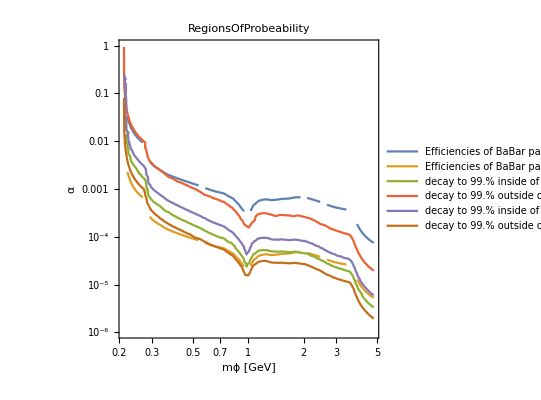

```mathematica
searchRegions[0,0.99]
```

```mathematica
probeability[BRχ_,perc_]:=Rasterize[ContourPlot[{cτϕBRDM[mϕ,α,BRχ]==0.5,cτϕBRDM[mϕ,α,BRχ]==100,(expDecay[dres,π/2,mϕ,α,BRχ]/.Belle2params)==perc,(expDecay[RCDC,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc,(expDecay[RKLM,π/2,mϕ,α,BRχ]/.Belle2params)==1-perc},{mϕ,2mμ/.masses,mB-mK/.masses},{α,10^-6,1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},ContourLabels->{"cτ=0.5cm","cτ=100cm","d_0=100µm","d_0=162cm","d_0=300cm"},PlotRange -> Full,PlotLegends->{"cτ=0.5cm","cτ=100cm",StringForm["d_0=100µm"], StringForm["d_0=162cm"],StringForm["d_0=300cm"]},AxesStyle->Black,LabelStyle->Directive[Black,14]]]
```

InterpolatingFunction::dmval: Input value {0.200046} lies outside the range of data in the interpolating function. Extrapolation will be used.

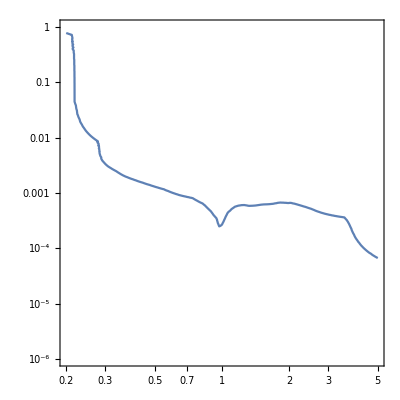

```mathematica
ContourPlot[cτϕBRDM[mϕ,α,0]==0.5,{mϕ,0.2,5},{α,10^-6,1},ScalingFunctions->{"Log","Log"},Exclusions->None]
```

```mathematica
probeability[0,0.99]
Export["results/probeability.png",%]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

results/probeability.png

```mathematica
cτϕBRDM[0.28,10^-4,0]//N
```

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

(2.×10^-14)/((5.76811×10^-18+0. ⅈ)+5.20297×10^-18 HeavisideTheta[0.])

```mathematica
FindRoot[cτϕBRDM[0.28,α,0]==100,{α,4 10^-4}]
```

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {-100.+(2.×10^-14)/((9.22897×10^-17+0. ⅈ)+8.32475×10^-17 HeavisideTheta[0.])} is not a list of numbers with dimensions {1} at {α} = {0.0004}.

FindRoot[cτϕBRDM[0.28,α,0]==100,{α,4/10^4}]

```mathematica
(* re-colour, label, get rid of holes *)
```

#### (n̄)_s

```mathematica
nsbar[mϕ_,α_,BRχ_]:=
NB (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]]  (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
Block[{NB=NBBBelleII/.Belle2params,γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},nsbar[1,10^-4,0]]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

31.5247+0. ⅈ

```mathematica
nsbarBelleII[mϕ_,α_,BRχ_]:=
NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle II *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelleIIpion[mϕ_,α_,BRχ_]:=
NBBBelleII (* number of BB pairs at Belle II *)BrBtoXsππBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kππ *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle II *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

```mathematica
nsbarBelle[mϕ_,α_,BRχ_]:=NBBBelle (* number of BB pairs at Belle II *)BrBtoXsμμBRDM[mϕ,α,BRχ] (* Branching ratio of B pair into Kμμ *)Block[{γβB=γβB /.Belleparams,θCDCMin=θCDCMin/.Belleparams,θCDCMax=θCDCMax/.Belleparams,RCDC=RCDC/.Belleparams,dres=dres/.Belleparams},GeomInt[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],1,50,cτϕBRDM[mϕ,α,BRχ],γβϕB[mϕ]] ](* geometry of 1-50 cm BaBar search region, but at Belle *) extrapeffBelleII[mϕ,α,BRχ] (* efficiency of BaBar rescaled to Belle II *) /.formFactors/.values/.masses/.couplings/.ckms/.Belleparams
```

```mathematica
ContourPlot[nsbarBelleII[m,α,NBBBelleII0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII",PlotLegends->Automatic,ColorFunction->ColorData["SolarColors"],Contours->Automatic]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {Ksvalues} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 5.43×10^-322+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.04338×10^-318+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.60241}. NIntegrate obtained 2.388×10^-320+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 2.7369×10^-307 (8.63509×10^-10+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.75466×10^-307 (0.000163264+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.61636×10^-305 (0.0000101501+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
PlotContoursManually[nsbarBelleII,0,2mμ/.masses,mB-mK/.masses,10^-6,1,1,5*10^7,{1,10,100,1000,10000,100000,1000000,10000000}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.60241}. NIntegrate obtained 3.2816×10^-320+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.14×10^-322+0. ⅈ and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.74749}. NIntegrate obtained 1.947×10^-321+0. ⅈ and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 7.87807×10^-308 (1.94292×10^-6+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.87584×10^-307 (0.0028948+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.88041×10^-308 (0.0000161648+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

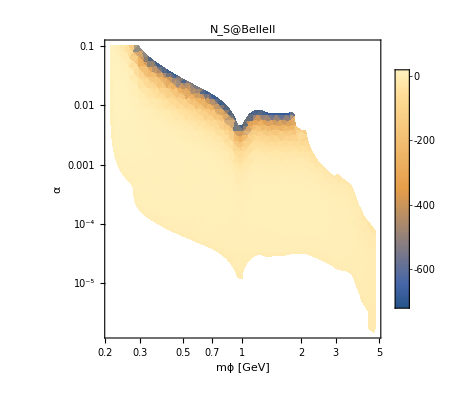

```mathematica
DensityPlot[Log[nsbarBelleII[m,α,0]]/.HeavisideTheta[0]:>1,{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"N_S@BelleII",PlotLegends->Automatic,AxesStyle->Black,FrameStyle->Black,LabelStyle->Directive[Black,14],PlotLegends->Automatic,Exclusions->None,PlotRange->All]
```

InterpolatingFunction::dmval: Input value {0.212047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

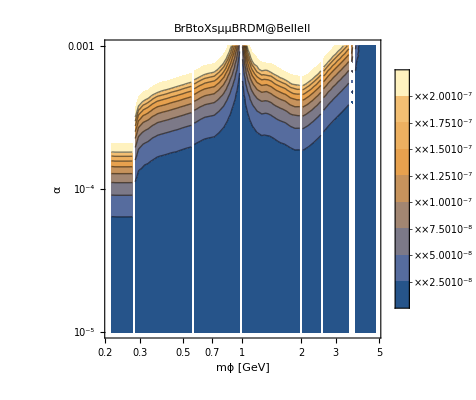

```mathematica
ContourPlot[BrBtoXsμμBRDM[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-5,10^-3},ScalingFunctions->{"Log","Log"},FrameLabel->{"mϕ [GeV]","α"},PlotLabel->"BrBtoXsμμBRDM@BelleII",PlotLegends->Automatic]
```

#### Exclusive 3-event line: μ

K^+

```mathematica
eventsBRtauBelleIIfullCDCmuonK[ma_,cc_,BRBtoKa_]:= (* a hundred percent efficiency and the full Belle II CDC as a search region *)Block[{γβB=γβB /.Belle2params,θCDCMin=θCDCMin/.Belle2params,θCDCMax=θCDCMax/.Belle2params,RCDC=RCDC/.Belle2params,dres=dres/.Belle2params},NBBBelleII (* number of BB pairs at Belle II *)BRBtoKa(* Branching ratio of B to K+a*) Γalpff[ma,mμ,cc]/Γalp[ma,cc] GeomIntBelleIICDC[θminBoost[θCDCMin,RCDC,cτB,γβB],θmaxBoost[θCDCMax,RCDC,cτB,γβB],dres,RCDC,cτa[ma,cc],γβϕB[ma]] ]/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params
```

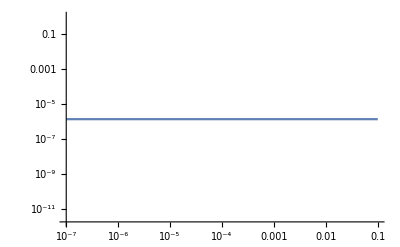

```mathematica
LogLogPlot[{Γalpff[2,mμ,cc]/Γalp[2,cc]/.values/.masses},{cc,10^-7,10^-1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.18088}. NIntegrate obtained 0.891515+0. ⅈ and 5.15396×10^-6 for the integral and error estimates.

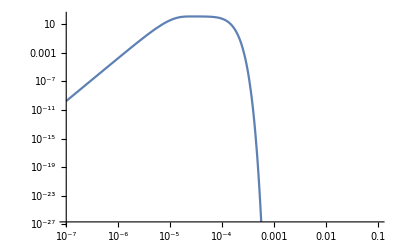

```mathematica
LogLogPlot[1.93eventsBRtauBelleIIfullCDCmuonK[2,cc,10^-3],{cc,10^-7,10^-1}]
```

```mathematica
Show[ContourPlot[1.93Abs[eventsBRtauBelleIIfullCDCmuonK[2,cc,BRBtoKa]],{cc,10^-6,10^-1},{BRBtoKa,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Black},ScalingFunctions->{"Log","Log"},FrameLabel->{"cc","BR(B -> Ka)"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full]]
```

InterpolatingFunction::dmval: Input value {0.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Show[ContourPlot[1.93Abs[eventsBRtauBelleIIfullCDCmuonK[3,cc,BRBtoKa]],{cc,10^-6,10^-1},{BRBtoKa,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourStyle->{Black},ScalingFunctions->{"Log","Log"},FrameLabel->{"cc","BR(B -> Ka)"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full]]
```

-Graphics-

Belle II, 3 events for muons+taus and pions. Decays to K+&K*

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.04223}. NIntegrate obtained 7.36645×10^7+0. ⅈ and 1.84782×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

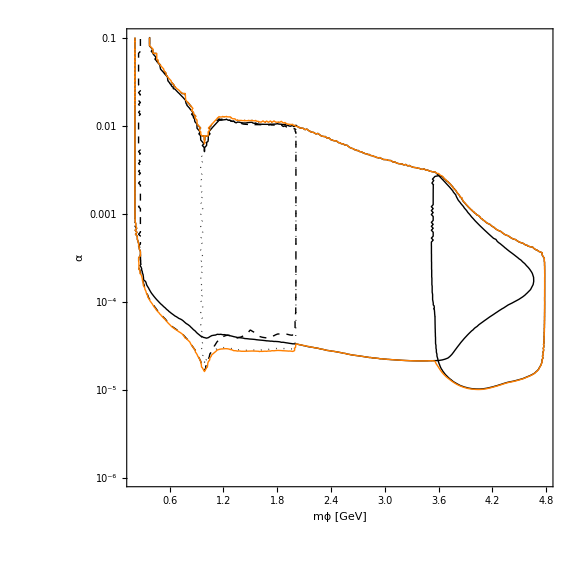

results/BelleII/BelleII_3events_muons-taus-pions-kaons_newboost_newGeomInt_S-PS-V-AV.png

```mathematica
Show[ContourPlot[1.93 nsbarBelleIIfullCDCmuonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCtauK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black,Thick},Contours->{3},PlotRange->Full],ContourPlot[1.93 nsbarBelleIIfullCDCpionK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dashed},Contours->{3}],ContourPlot[1.93 nsbarBelleIIfullCDCkaonK[m,α,0],{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Black, Dotted},Contours->{3},PlotRange->Full],
ContourPlot[1.93 (nsbarBelleIIfullCDCkaonK[m,α,0]+nsbarBelleIIfullCDCpionK[m,α,0]+nsbarBelleIIfullCDCmuonK[m,α,0]+nsbarBelleIIfullCDCtauK[m,α,0]),{m,2mμ/.masses,mB-mK/.masses},{α,10^-6,10^-1},ScalingFunctions->{None,"Log"},FrameLabel->{"mϕ [GeV]","α"},ContourShading->None,ContourStyle->{Orange},Contours->{3},PlotRange->Full],ImageSize-> Large]
Export["results/BelleII/alp-BelleII_3events_muons-taus-pions-kaons_newboost_newGeomInt.png",%]
```